```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 59 Kb

{Utilities`CleanSlate`,GeneralRelativityTensors`,GeneralRelativityTensors`CommonTensors`,GeneralRelativityTensors`TensorDerivatives`,GeneralRelativityTensors`TensorManipulation`,GeneralRelativityTensors`TensorDefinitions`,GeneralRelativityTensors`Utils`,Notation`,VariationalMethods`,System`,Global`}

```mathematica
<<GeneralRelativityTensors`
```

```mathematica
<<Notation`
```

```mathematica
Clear[lineTometric]
lineTometric[lineelement_ , differentials_]:= 
Table[If[i==j ,Coefficient[lineelement, differentials[[i]] differentials[[j]]],
(1/2)*Coefficient[lineelement, differentials[[i]] differentials[[j]]]],
{i,1,Length[differentials]},{j,1,Length[differentials]}]  ;
```

```mathematica
Symbolize[Subscript[Z, 0]]
Symbolize[Subscript[Z, 1]]
Symbolize[Subscript[Z, 2]]
Symbolize[Subscript[Z, 3]]
Symbolize[Subscript[Z, 4]]
Symbolize[Subscript[η, 0]]
Symbolize[Subscript[t, 0]]
Symbolize[Subscript[t, -1]]
Symbolize[Subscript[t, b]]
Symbolize[Subscript[z, b]]
Symbolize[Subscript[t, k]]
Symbolize[Subscript[z, k]]
Symbolize[ξ̄]
(* Symbolize[d ξ̄] *)  (* Figure out why this doesn't work - overbar over both d and ξ will work? *)
```

```mathematica
CreatePalette[{ 
PasteButton[Subscript[Z, 0]],
 PasteButton[Subscript[Z, 1]] , 
PasteButton[Subscript[Z, 2]] ,
PasteButton[Subscript[Z, 3]] ,
PasteButton[Subscript[Z, 4]] ,
PasteButton[Subscript[η, 0]] ,
PasteButton[Subscript[t, 0]] ,
PasteButton[Subscript[t, -1]] ,
PasteButton[Subscript[t, b]] ,
PasteButton[Subscript[z, b]] ,
PasteButton[Subscript[t, k]] ,
PasteButton[Subscript[z, k]] ,
PasteButton[ξ̄]
}
]
```

jv7ds_shm28FrontEndObject[LinkObject["jv7ds_shm", 3, 1]]28Untitled-2

```mathematica
Clear[dtReplace]
dtReplace = {
Dt[Subscript[Z, 0]] -> Subscript[dZ, 0] ,
Dt[Subscript[Z, 1]] -> Subscript[dZ, 1] ,
Dt[Subscript[Z, 2]]-> Subscript[dZ, 2] ,
Dt[Subscript[Z, 3]]-> Subscript[dZ, 3] ,
Dt[Subscript[Z, 4]] -> Subscript[dZ, 4] ,
 Dt[Subscript[η, 0]]-> Subscript[dη, 0] , 
 Dt[Subscript[t, 0]]-> Subscript[dt, 0] , 
 Dt[t]-> dt ,
 Dt[T]-> dT ,
Dt[χ] -> dχ , 
 Dt[θ] -> dθ , 
Dt[ϕ] -> dϕ  ,
Dt[η] -> dη  ,
Dt[R] -> dR  ,
Dt[x]-> dx , 
Dt[y] -> dy , 
Dt[z]-> dz  ,
Dt[Subscript[t, -1]]-> Subscript[dt, -1] , 
Dt[Subscript[t, b]]-> Subscript[dt, b] ,
Dt[Subscript[z, b]]-> Subscript[dz, b] ,
Dt[Subscript[t, k]] -> Subscript[dt, k] ,
Dt[Subscript[z, k]] -> Subscript[dz, k] , 
Dt[ρ] -> dρ ,
Dt[𝒰]-> d𝒰 , 
Dt[𝒱]-> d𝒱 , 
Dt[ξ]-> dξ , 
Dt[ξ̄]-> d ξ̄
} ;
dtReplace // TableForm
```

Dt[Z_0]→dZ_0
Dt[Z_1]→dZ_1
Dt[Z_2]→dZ_2
Dt[Z_3]→dZ_3
Dt[Z_4]→dZ_4
Dt[η_0]→dη_0
Dt[t_0]→dt_0
Dt[t]→dt
Dt[T]→dT
Dt[χ]→dχ
Dt[θ]→dθ
Dt[ϕ]→dϕ
Dt[η]→dη
Dt[R]→dR
Dt[x]→dx
Dt[y]→dy
Dt[z]→dz
Dt[t_-1]→dt_-1
Dt[t_b]→dt_b
Dt[z_b]→dz_b
Dt[t_k]→dt_k
Dt[z_k]→dz_k
Dt[ρ]→dρ
Dt[𝒰]→d𝒰
Dt[𝒱]→d𝒱
Dt[ξ]→dξ
Dt[ξ̄]→d ξ̄

```mathematica
Clear[eulerLagrangeEquations]
eulerLagrangeEquations[metric_, variables_ , parameter_ ]:= Module[
{q,qReplace,ℒ,eqs,eulerEquations} , 
Clear[q] ;
q = 
Flatten[Table[Map[variables[[i]],{parameter}] , {i,1,Length[variables]}]] ;
Clear[qReplace] ;
qReplace = 
Thread[
variables -> q ] ;
Clear[ℒ] ;
ℒ = 
Sum[(metric /. qReplace)[[i,j]] *   D[q,parameter][[i]] D[q,parameter][[j]] , {i,1, Length[q]},{j,1,Length[q]}] ;
Clear[eqs] ;
eqs = 
Table[
D[ D[ ℒ ,  D[q[[i]], parameter]] , parameter ] -D[ ℒ ,  q[[i]]]  , 
{i,1,Length[q]}] // Expand   ;
Clear[eulerEquations] ;
eulerEquations = 
Table[
Sum[
( Expand[eqs[[j]]][[i]] / Coefficient[eqs[[j]] ,D[D[q[[j]], parameter], parameter]]   ) , {i,1,Length[ Expand[eqs[[j]]]] } ] ,
{j,1,4}]  
];
```

```mathematica
a/:Dt[a]=0  ;
Λ/:Dt[Λ]=0  ;
(* Differential of a is zero , a is a constant , etc.  *)
```

```mathematica
Clear[input] 
input[equationNumber_,equation_,metricName_,displayName_,variables_,indices_]:= Module[{},
Clear[tensorList];
tensorList = {
"g"<>equationNumber,
"christoffel"<>equationNumber , 
"riemann"<>equationNumber  ,
"ricci"<>equationNumber ,
"ricciscalar"<>equationNumber,
"kretschmannscalar"<>equationNumber  ,
"einstein"<>equationNumber  , 
"weyl"<>equationNumber  ,
"cotton"<>equationNumber  
};
tensorList[[1]] = 
ToMetric[{ metricName, displayName } , variables, equation, indices ] ;
tensorList[[2]]  = 
ChristoffelSymbol[ tensorList[[1]] , ActWith-> Simplify] ;
tensorList[[3]] = 
RiemannTensor[ tensorList[[1]] , ActWithNested-> Simplify ];
tensorList[[4]] = 
RicciTensor[ tensorList[[1]] , ActWith-> Simplify ] ;
tensorList[[5]] = 
RicciScalar[ tensorList[[1]] , ActWith-> Simplify ] ;
 tensorList[[6]] = 
KretschmannScalar[ tensorList[[1]] , ActWith-> Simplify] ;  
 tensorList[[7]] = 
EinsteinTensor[ tensorList[[1]] , ActWith-> Simplify] ;    
tensorList[[8]] = 
WeylTensor[ tensorList[[1]] , ActWith-> Simplify ] ;
 tensorList[[9]] = 
CottonTensor[ tensorList[[1]] , ActWith-> Simplify ] ; 
];
```

```mathematica
Clear[lineElement] (* Page 41 , eq4pt2 *) 
lineElement = - Subscript[dZ, 0]^2 + Subscript[dZ, 1]^2+ Subscript[dZ, 2]^2+Subscript[dZ, 3]^2+Subscript[dZ, 4]^2
```

-dZ_0^2+dZ_1^2+dZ_2^2+dZ_3^2+dZ_4^2

```mathematica
Clear[hyperboloid4pt1]
hyperboloid4pt1 = 
- Subscript[Z, 0]^2+ Subscript[Z, 1]^2+Subscript[Z, 2]^2+Subscript[Z, 3]^2+Subscript[Z, 4]^2== a^2 (* /. a->√(3/Λ) uncomment if needed *)
```

-Z_0^2+Z_1^2+Z_2^2+Z_3^2+Z_4^2==a^2

```mathematica
Clear[transform4pt3]
transform4pt3 = {
Subscript[Z, 0]-> a Sinh[t/a] ,
Subscript[Z, 1]-> a Cosh[t/a] Cos[χ] ,
Subscript[Z, 2]-> a Cosh[t/a] Sin[χ] Cos[θ] ,
Subscript[Z, 3]-> a Cosh[t/a] Sin[χ] Sin[θ] Cos[ϕ] ,
Subscript[Z, 4]-> a Cosh[t/a] Sin[χ] Sin[θ] Sin[ϕ]
} ;
transform4pt3 // TableForm
```

Z_0→a Sinh[t/a]
Z_1→a Cos[χ] Cosh[t/a]
Z_2→a Cos[θ] Cosh[t/a] Sin[χ]
Z_3→a Cos[ϕ] Cosh[t/a] Sin[θ] Sin[χ]
Z_4→a Cosh[t/a] Sin[θ] Sin[ϕ] Sin[χ]

```mathematica
hyperboloid4pt1 
hyperboloid4pt1  //. transform4pt3
hyperboloid4pt1  //. transform4pt3  // Simplify (* true *)
```

-Z_0^2+Z_1^2+Z_2^2+Z_3^2+Z_4^2==a^2

a^2 Cos[χ]^2 Cosh[t/a]^2+a^2 Cos[θ]^2 Cosh[t/a]^2 Sin[χ]^2+a^2 Cos[ϕ]^2 Cosh[t/a]^2 Sin[θ]^2 Sin[χ]^2+a^2 Cosh[t/a]^2 Sin[θ]^2 Sin[ϕ]^2 Sin[χ]^2-a^2 Sinh[t/a]^2==a^2

True

```mathematica
Dt[ transform4pt3 ] /. dtReplace // TableForm
```

dZ_0→dt Cosh[t/a]
dZ_1→-a dχ Cosh[t/a] Sin[χ]+dt Cos[χ] Sinh[t/a]
dZ_2→a dχ Cos[θ] Cos[χ] Cosh[t/a]-a dθ Cosh[t/a] Sin[θ] Sin[χ]+dt Cos[θ] Sin[χ] Sinh[t/a]
dZ_3→a dχ Cos[ϕ] Cos[χ] Cosh[t/a] Sin[θ]+a dθ Cos[θ] Cos[ϕ] Cosh[t/a] Sin[χ]-a dϕ Cosh[t/a] Sin[θ] Sin[ϕ] Sin[χ]+dt Cos[ϕ] Sin[θ] Sin[χ] Sinh[t/a]
dZ_4→a dχ Cos[χ] Cosh[t/a] Sin[θ] Sin[ϕ]+a dϕ Cos[ϕ] Cosh[t/a] Sin[θ] Sin[χ]+a dθ Cos[θ] Cosh[t/a] Sin[ϕ] Sin[χ]+dt Sin[θ] Sin[ϕ] Sin[χ] Sinh[t/a]

```mathematica
Clear[lineToMetric]
lineToMetric[lineelement_ , differentials_]:= 
Table[If[i==j ,Coefficient[lineelement, differentials[[i]] differentials[[j]]],
(1/2)*Coefficient[lineelement, differentials[[i]] differentials[[j]]]],
{i,1,Length[differentials]},{j,1,Length[differentials]}]  ;
```

```mathematica
Clear[metric4pt4](* remember a in this case is √(3/Λ) *) 
metric4pt4 = 
lineToMetric[
( Collect[ ( lineElement /. ( Dt[ transform4pt3 ] /. dtReplace ) // Expand ) , { dt^2, dχ^2, dθ^2, dϕ^2 } ]  ) , { dt , dχ , dθ , dϕ } ]    // Simplify ;
metric4pt4 // MatrixForm
```

(-1 | 0 | 0 | 0
0 | a^2 Cosh[t/a]^2 | 0 | 0
0 | 0 | a^2 Cosh[t/a]^2 Sin[χ]^2 | 0
0 | 0 | 0 | a^2 Cosh[t/a]^2 Sin[θ]^2 Sin[χ]^2)

```mathematica
Clear[inverse4pt4]
inverse4pt4 = 
Inverse[ metric4pt4 ] ;
inverse4pt4 // MatrixForm
```

(-1 | 0 | 0 | 0
0 | Sech[t/a]^2/a^2 | 0 | 0
0 | 0 | (Csc[χ]^2 Sech[t/a]^2)/a^2 | 0
0 | 0 | 0 | (Csc[θ]^2 Csc[χ]^2 Sech[t/a]^2)/a^2)

```mathematica
input[ "metric4pt4", metric4pt4, "4pt4","g^dS",{t,χ,θ,ϕ}, "Greek"] // Timing
```

{3.82885,Null}

```mathematica
TensorValues[tensorList[[1]]] // MatrixForm // pdConv
```

(-1 | 0 | 0 | 0
0 | a^2 cosh^2(t/a) | 0 | 0
0 | 0 | a^2 sin^2(χ) cosh^2(t/a) | 0
0 | 0 | 0 | a^2 sin^2(θ) sin^2(χ) cosh^2(t/a))

```mathematica
TensorValues[tensorList[[2]]] // MatrixForm // pdConv
```

((0
0
0
0) | (0
1/2 a sinh((2 t)/a)
0
0) | (0
0
1/2 a sin^2(χ) sinh((2 t)/a)
0) | (0
0
0
1/2 a sin^2(θ) sin^2(χ) sinh((2 t)/a))
(0
(tanh(t/a))/a
0
0) | ((tanh(t/a))/a
0
0
0) | (0
0
sin(χ) (-cos(χ))
0) | (0
0
0
sin^2(θ) sin(χ) (-cos(χ)))
(0
0
(tanh(t/a))/a
0) | (0
0
cot(χ)
0) | ((tanh(t/a))/a
cot(χ)
0
0) | (0
0
0
sin(θ) (-cos(θ)))
(0
0
0
(tanh(t/a))/a) | (0
0
0
cot(χ)) | (0
0
0
cot(θ)) | ((tanh(t/a))/a
cot(χ)
cot(θ)
0))

```mathematica
TensorValues[tensorList[[3]]] // MatrixForm // pdConv
```

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | -cosh^2(t/a) | 0 | 0
cosh^2(t/a) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | sin^2(χ) (-cosh^2(t/a)) | 0
0 | 0 | 0 | 0
sin^2(χ) cosh^2(t/a) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | sin^2(θ) sin^2(χ) (-cosh^2(t/a))
0 | 0 | 0 | 0
0 | 0 | 0 | 0
sin^2(θ) sin^2(χ) cosh^2(t/a) | 0 | 0 | 0)
(0 | cosh^2(t/a) | 0 | 0
-cosh^2(t/a) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | a^2 sin^2(χ) cosh^4(t/a) | 0
0 | -a^2 sin^2(χ) cosh^4(t/a) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | a^2 sin^2(θ) sin^2(χ) cosh^4(t/a)
0 | 0 | 0 | 0
0 | -a^2 sin^2(θ) sin^2(χ) cosh^4(t/a) | 0 | 0)
(0 | 0 | sin^2(χ) cosh^2(t/a) | 0
0 | 0 | 0 | 0
sin^2(χ) (-cosh^2(t/a)) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | -a^2 sin^2(χ) cosh^4(t/a) | 0
0 | a^2 sin^2(χ) cosh^4(t/a) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | a^2 sin^2(θ) sin^4(χ) cosh^4(t/a)
0 | 0 | -a^2 sin^2(θ) sin^4(χ) cosh^4(t/a) | 0)
(0 | 0 | 0 | sin^2(θ) sin^2(χ) cosh^2(t/a)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
sin^2(θ) sin^2(χ) (-cosh^2(t/a)) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | -a^2 sin^2(θ) sin^2(χ) cosh^4(t/a)
0 | 0 | 0 | 0
0 | a^2 sin^2(θ) sin^2(χ) cosh^4(t/a) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -a^2 sin^2(θ) sin^4(χ) cosh^4(t/a)
0 | 0 | a^2 sin^2(θ) sin^4(χ) cosh^4(t/a) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
TensorValues[tensorList[[4]]] // MatrixForm // pdConv
```

(-3/a^2 | 0 | 0 | 0
0 | 3 cosh^2(t/a) | 0 | 0
0 | 0 | 3 sin^2(χ) cosh^2(t/a) | 0
0 | 0 | 0 | 3 sin^2(θ) sin^2(χ) cosh^2(t/a))

```mathematica
TensorValues[tensorList[[5]]] // MatrixForm // pdConv
```

12/a^2

```mathematica
TensorValues[tensorList[[6]]] // MatrixForm // pdConv
```

24/a^4

```mathematica
TensorValues[tensorList[[7]]] // MatrixForm // pdConv
```

(3/a^2 | 0 | 0 | 0
0 | -3 cosh^2(t/a) | 0 | 0
0 | 0 | -3 sin^2(χ) cosh^2(t/a) | 0
0 | 0 | 0 | -3 sin^2(θ) sin^2(χ) cosh^2(t/a))

```mathematica
TensorValues[tensorList[[8]]] // MatrixForm // pdConv
```

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
TensorValues[tensorList[[9]]] // MatrixForm // pdConv
```

((0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0))

```mathematica
Clear[ℓ] 
ℓ = 
(1/(√2))*{ PowerExpand[Sqrt[-metric4pt4[[1,1]]]] ,PowerExpand[Sqrt[metric4pt4[[2,2]]]] ,0,0}
```

{1/(√2),(a Cosh[t/a])/(√2),0,0}

```mathematica
Clear[𝓃]
𝓃 =
(1/(√2))*{ PowerExpand[Sqrt[-metric4pt4[[1,1]]]] , -PowerExpand[Sqrt[metric4pt4[[2,2]]]] ,0,0}
```

{1/(√2),-(a Cosh[t/a])/(√2),0,0}

```mathematica
Clear[𝓂]
𝓂 =
(1/(√2))*{0,0, PowerExpand[Sqrt[metric4pt4[[3,3]]]] , ⅈ PowerExpand[Sqrt[metric4pt4[[4,4]]]] }
```

{0,0,(a Cosh[t/a] Sin[χ])/(√2),(ⅈ a Cosh[t/a] Sin[θ] Sin[χ])/(√2)}

```mathematica
Clear[𝓂bar]
𝓂bar =
(1/(√2))*{0,0, PowerExpand[Sqrt[metric4pt4[[3,3]]]] , -ⅈ PowerExpand[Sqrt[metric4pt4[[4,4]]]] }
```

{0,0,(a Cosh[t/a] Sin[χ])/(√2),-(ⅈ a Cosh[t/a] Sin[θ] Sin[χ])/(√2)}

```mathematica
(* ALWAYS ALWAYS ALWAYS CHECK IF INDICES ARE UP OR DOWN !!!!! *)
l = ToTensor[ {"NewTensor" , "l"} , tensorList[[1]] , ℓ , {-μ}]
n = ToTensor[{"NewTensor" , "n" } , tensorList[[1]] , 𝓃 , {-μ} ] 
m = ToTensor[{"NewTensor" , "m" } , tensorList[[1]] , 𝓂 , {-μ} ] 
mbar = ToTensor[{"NewTensor" , "mbar" } , tensorList[[1]] , 𝓂bar , {-μ} ]
```

l_μ^

n_μ^

m_μ^

mbar_μ^

```mathematica
TensorValues[ContractIndices[l[-μ]l[μ]]] == 0  // Expand // Simplify 
TensorValues[ContractIndices[n[-μ]n[μ]] ]== 0  // Expand // Simplify 
TensorValues[ContractIndices[m[-μ]m[μ]]] == 0   // Expand // FullSimplify 
TensorValues[ContractIndices[mbar[-μ]mbar[μ]]] == 0  // Expand // FullSimplify 
TensorValues[ContractIndices[l[-μ]n[μ]]] == -1// Expand // FullSimplify 
TensorValues[ContractIndices[l[μ]n[-μ]]] == -1  // Expand // FullSimplify 
TensorValues[ContractIndices[m[-μ]mbar[μ]]] ==  1 // Expand // FullSimplify 
TensorValues[ContractIndices[m[μ]mbar[-μ]]] ==  1 // Expand // FullSimplify 
Clear[completenessDownIndices]
completenessDownIndices = 
MergeTensors[-l[-μ]n[-ν]-n[-μ]l[-ν] + m[-μ]mbar[-ν]+m[-ν]mbar[-μ]]  ;
TensorValues[ completenessDownIndices ]  // MatrixForm

Thread[Flatten[metric4pt4] == 
Flatten[ TensorValues[ completenessDownIndices ]] ] // Expand // FullSimplify 

Clear[completenessUpIndices]
completenessUpIndices = 
MergeTensors[-l[μ]n[ν]-n[μ]l[ν] + m[μ]mbar[ν]+ m[ν]mbar[μ]]  ;
TensorValues[ completenessUpIndices ]  // MatrixForm

Thread[Flatten[inverse4pt4] == 
Flatten[ TensorValues[ completenessUpIndices ]] ]  // Expand // FullSimplify
```

True

True

True

«5 more identical outputs»

(-1 | 0 | 0 | 0
0 | a^2 Cosh[t/a]^2 | 0 | 0
0 | 0 | a^2 Cosh[t/a]^2 Sin[χ]^2 | 0
0 | 0 | 0 | a^2 Cosh[t/a]^2 Sin[θ]^2 Sin[χ]^2)

True

(-1 | 0 | 0 | 0
0 | Sech[t/a]^2/a^2 | 0 | 0
0 | 0 | (Csc[χ]^2 Sech[t/a]^2)/a^2 | 0
0 | 0 | 0 | (Csc[θ]^2 Csc[χ]^2 Sech[t/a]^2)/a^2)

True

```mathematica
Clear[spinCoefficientReplace]  (* Page 56 Wang *) (* check where these definitions came from *)
spinCoefficientReplace= {
ρ ->(  MergeTensors[ CovariantD[ l[-μ],-ν] m[μ] mbar[ν] ] // TensorValues  // Expand // FullSimplify )  , 
μ-> (*note minus sign *)(-1)*( MergeTensors [ CovariantD[ n[-μ] , -ν ] mbar[μ] m[ν] ] // TensorValues  // Expand  // FullSimplify )  , 
ε -> ( (1/2)(( MergeTensors[CovariantD[l[-μ],-ν] n[μ] l[ν]] // TensorValues  // Expand  // FullSimplify  )  - 
(MergeTensors[ CovariantD[ m[-μ],-ν] mbar[μ] l[ν]] // TensorValues // Expand // FullSimplify) ) // Expand  // FullSimplify ) , 
γ -> (* something weird here correct definition off by minus sign *) ((1/2)((MergeTensors[CovariantD[ l[-μ],-ν] n[μ]n[ν] ] // TensorValues  // Expand  )-
(MergeTensors[CovariantD[ m[-μ],-ν] mbar[μ] n[ν]] // TensorValues // Expand  // FullSimplify )) // Expand ) , 
σ->( MergeTensors[ CovariantD[l[-μ] , -ν] m[μ] m[ν]] // TensorValues  // Expand // FullSimplify)  , 
λ-> (* note minus sign *)(-1)*( MergeTensors[ CovariantD[ n[-μ],-ν] mbar[μ] mbar[ν] ]  // TensorValues // Expand // FullSimplify)  ,
κ->(  MergeTensors[ CovariantD[ l[-μ] ,-ν] m[μ] l[ν]  ]  // TensorValues ) , 
ν-> ( MergeTensors[ CovariantD[ n[-μ],-ν]m[μ] n[ν] ] // TensorValues ) , 
τ->( MergeTensors[ CovariantD[ l[-μ],-ν] m[μ] n[ν ]]// TensorValues ) , 
π-> (* Note minus sign *)(-1)* (MergeTensors[CovariantD[ n[-μ],-ν] mbar[μ] l[ν]] // TensorValues  // Expand ) , 
α-> ((1/2)((MergeTensors[CovariantD[ l[-μ],-ν] n[μ] mbar[ν]] // TensorValues )-
(MergeTensors[CovariantD[ m[-μ],-ν] mbar[μ] mbar[ν]] // TensorValues)) ) , 
β -> (* Spin coefficient β *) 
((1/2)((MergeTensors[ CovariantD[ l[-μ],-ν] n[μ]m[ν]] // TensorValues)- 
(MergeTensors[CovariantD[ m[-μ],-ν] mbar[μ] m[ν]] // TensorValues )))
} ;
spinCoefficientReplace // TableForm // pdConv
```

ρ→(cot(χ) sech(t/a)-tanh(t/a))/(√2 a)
μ→(cot(χ) sech(t/a)+tanh(t/a))/(√2 a)
ε→(tanh(t/a))/(2 √2 a)
γ→-(tanh(t/a))/(2 √2 a)
σ→0
λ→0
κ→0
ν→0
τ→0
π→0
α→(cot(θ) csc(χ) sech(t/a))/(2 √2 a)
β→-(cot(θ) csc(χ) sech(t/a))/(2 √2 a)

```mathematica
Clear[ricciScalarsReplace] (* Definitions from Griffiths *) 
(* Page 57 Wang *) 
ricciScalarsReplace = {
Subscript[Φ, oo]-> (* be careful about oh's not zeros *) 
(-1/2)*TensorValues[MergeTensors[tensorList[[4]][-μ,-ν]l[μ]l[ν]]] // Expand // FullSimplify  , 
Subscript[Φ, O1]-> 
(-1/2)*TensorValues[MergeTensors[tensorList[[4]][-μ,-ν]l[μ]m[ν]]] // Expand // FullSimplify, 
Subscript[Φ, O2]-> 
(-1/2)*TensorValues[MergeTensors[tensorList[[4]][-μ,-ν]m[μ]m[ν]]] // Expand // FullSimplify, 
Subscript[Φ, 11]-> 
(-1/4)*( ( TensorValues[MergeTensors[tensorList[[4]][-μ,-ν]l[μ]n[ν]]])+ (TensorValues[MergeTensors[tensorList[[4]][-μ,-ν]m[μ]mbar[ν]]])) // Expand // FullSimplify, 
Subscript[Φ, 12]-> 
(-1/2)*TensorValues[MergeTensors[tensorList[[4]][-μ,-ν]n[μ]m[ν]]] // Expand // FullSimplify, 
Subscript[Φ, 22]-> 
(-1/2)*TensorValues[MergeTensors[tensorList[[4]][-μ,-ν]n[μ]n[ν]]]// Expand // FullSimplify , 
Λ-> 
(1/24)*TensorValues[tensorList[[5]]]// Expand // FullSimplify
} ;
ricciScalarsReplace  // TableForm // pdConv
```

Φ_oo→0
Φ_O1→0
Φ_O2→0
Φ_11→0
Φ_12→0
Φ_22→0
Λ→1/(2 a^2)

```mathematica
Clear[weylScalarsReplace](* Definitions from Griffiths *) 
(* Page 57 Wang *) 
weylScalarsReplace = {

Subscript[Ψ, 0]-> (-1)*TensorValues[MergeTensors[tensorList[[8]][-κ,-λ,-μ,-ν]l[κ]m[λ]l[μ]m[ν]]]// Expand // FullSimplify , 
Subscript[Ψ, 1]-> (-1)*TensorValues[MergeTensors[tensorList[[8]][-κ,-λ,-μ,-ν]l[κ]n[λ]l[μ]m[ν]]]// Expand // FullSimplify , 
Subscript[Ψ, 2]-> (-1)*TensorValues[MergeTensors[tensorList[[8]][-κ,-λ,-μ,-ν]l[κ]m[λ]mbar[μ]n[ν]]] // Expand // FullSimplify, 
Subscript[Ψ, 3]-> (-1)*TensorValues[MergeTensors[tensorList[[8]][-κ,-λ,-μ,-ν]n[κ]l[λ]n[μ]mbar[ν]]]// Expand // FullSimplify , 
Subscript[Ψ, 4]-> (-1)*TensorValues[MergeTensors[tensorList[[8]][-κ,-λ,-μ,-ν]n[κ]mbar[λ]n[μ]mbar[ν]]]// Expand // FullSimplify
} ;
weylScalarsReplace // TableForm // pdConv
```

Ψ_0→0
Ψ_1→0
Ψ_2→0
Ψ_3→0
Ψ_4→0

```mathematica
Clear[differentials]
differentials = { dt , dχ , dθ , dϕ }
```

{dt,dχ,dθ,dϕ}

```mathematica
Clear[lineElement4pt4]
lineElement4pt4 = Sum[ metric4pt4[[i,i]]* ( differentials[[i]] )^2 , { i , 1 , 4 } ]  // Simplify
```

-dt^2+a^2 Cosh[t/a]^2 (dχ^2+(dθ^2+dϕ^2 Sin[θ]^2) Sin[χ]^2)

```mathematica
Clear[fig4pt1]
fig4pt1 = 
( hyperboloid4pt1 /. Subscript[Z, 3]-> 0  /.  Subscript[Z, 4]-> 0    /. Λ-> 3  /. a-> 1 )
```

-Z_0^2+Z_1^2+Z_2^2==1

```mathematica
ContourPlot3D[Evaluate[ fig4pt1] , { Subscript[Z, 0] , -10 , 10 } , { Subscript[Z, 1] , -10 , 10 } , { Subscript[Z, 2] , -10 , 10 },Mesh-> None  ]
```

-Graphics3D-

```mathematica
fig4pt1  /. transform4pt3  /. χ -> 1  // Simplify 
( Subscript[Z, 0] /. transform4pt3  /. a-> 1  /. t -> 1  ) 
( Subscript[Z, 1]/. transform4pt3   /. a-> 1  /. χ-> 1  )^2
( Subscript[Z, 2]/. transform4pt3   /. a-> 1  /. χ-> 1  )^2
```

a^2 Cosh[t/a]^2 (Cos[1]^2+Cos[θ]^2 Sin[1]^2)==1+a^2 Sinh[t/a]^2

Sinh[1]

Cos[1]^2 Cosh[t]^2

Cos[θ]^2 Cosh[t]^2 Sin[1]^2

```mathematica
Solve[ ( fig4pt1   /. Subscript[Z, 0]->  ( Subscript[Z, 0] /. transform4pt3  /. a-> 1  /. t -> 1  ) )  ,Subscript[Z, 2] ][[2]]
```

{Z_2→√(1-Z_1^2+Sinh[1]^2)}

```mathematica
ContourPlot3D[ x^2+y^2-z^2== 1 , {x,-10,10},{y,-10,10},{z,-10,10},MeshFunctions->{#1^2+#2^2&,#1^2-#3^2&},MeshStyle->{Purple, Orange},Lighting->"Neutral",ContourStyle->Gray]
(* REDO THIS *)
```

-Graphics3D-

```mathematica
(* use this as an example *) 
ContourPlot3D[x^2-y^2==z,{x,-1,1},{y,-1,1},{z,-1,1},MeshFunctions->{#1-#2&,#1+#2&},MeshShading->{{Yellow,Blue},{Green,Cyan}}]
```

-Graphics3D-

```mathematica
(* Use as example *) 
ContourPlot3D[x^2-y^2==z,{x,-1,1},{y,-1,1},{z,-1,1},MeshFunctions->{#1-#2&,#1+#2&},MeshStyle->{Purple, Orange},Lighting->"Neutral",ContourStyle->Gray]
```

-Graphics3D-

```mathematica
?MeshFunctions
```

```mathematica
(* Example *) 
SliceContourPlot3D[Exp[-(x^2+y^2+z^2)],x^3+y^2-z^2==0,{x,-2,2},{y,-2,2},{z,-2,2}]
```

-Graphics3D-

```mathematica
Clear[transform4pt5a](* be careful further down - is η a function of t? *) 
transform4pt5a = 
Sin[η]== Sech[t/a]
```

Sin[η]==Sech[t/a]

```mathematica
Clear[transform4pt5]
transform4pt5 = 
Solve[ transform4pt5a , t ][[2]]  /. C[1]-> 0
```

{t→a ArcCosh[Csc[η]]}

```mathematica
(* If needed *) 
Flatten[Solve[ transform4pt5a , η ]][[2]]  /. C[1]-> 0
```

η→ArcSin[Sech[t/a]]

```mathematica
Dt[ transform4pt5 ]  /. dtReplace
```

{dt→-(a dη Cot[η] Csc[η])/(√(-1+Csc[η]) √(1+Csc[η]))}

```mathematica
(* The long way just to see if it works *) 
( Dt[ transform4pt3 ]/. dtReplace    ) /.( Dt[ transform4pt5 ]  /. dtReplace )  // TableForm
```

dZ_0→-(a dη Cosh[t/a] Cot[η] Csc[η])/(√(-1+Csc[η]) √(1+Csc[η]))
dZ_1→-a dχ Cosh[t/a] Sin[χ]-(a dη Cos[χ] Cot[η] Csc[η] Sinh[t/a])/(√(-1+Csc[η]) √(1+Csc[η]))
dZ_2→a dχ Cos[θ] Cos[χ] Cosh[t/a]-a dθ Cosh[t/a] Sin[θ] Sin[χ]-(a dη Cos[θ] Cot[η] Csc[η] Sin[χ] Sinh[t/a])/(√(-1+Csc[η]) √(1+Csc[η]))
dZ_3→a dχ Cos[ϕ] Cos[χ] Cosh[t/a] Sin[θ]+a dθ Cos[θ] Cos[ϕ] Cosh[t/a] Sin[χ]-a dϕ Cosh[t/a] Sin[θ] Sin[ϕ] Sin[χ]-(a dη Cos[ϕ] Cot[η] Csc[η] Sin[θ] Sin[χ] Sinh[t/a])/(√(-1+Csc[η]) √(1+Csc[η]))
dZ_4→a dχ Cos[χ] Cosh[t/a] Sin[θ] Sin[ϕ]+a dϕ Cos[ϕ] Cosh[t/a] Sin[θ] Sin[χ]+a dθ Cos[θ] Cosh[t/a] Sin[ϕ] Sin[χ]-(a dη Cot[η] Csc[η] Sin[θ] Sin[ϕ] Sin[χ] Sinh[t/a])/(√(-1+Csc[η]) √(1+Csc[η]))

```mathematica
( ( ( Dt[ transform4pt3 ]/. dtReplace    ) /.( Dt[ transform4pt5 ]  /. dtReplace )  ) /. transform4pt5 )  // Simplify // TableForm
```

dZ_0→-(a dη Cot[η] Csc[η]^2)/(√(-1+Csc[η]) √(1+Csc[η]))
dZ_1→-a Csc[η] (dη Cos[χ] Cot[η]+dχ Sin[χ])
dZ_2→-a Csc[η] (dθ Sin[θ] Sin[χ]+Cos[θ] (-dχ Cos[χ]+dη Cot[η] Sin[χ]))
dZ_3→a Csc[η] (-dϕ Sin[θ] Sin[ϕ] Sin[χ]+Cos[ϕ] (dχ Cos[χ] Sin[θ]+(dθ Cos[θ]-dη Cot[η] Sin[θ]) Sin[χ]))
dZ_4→a Csc[η] (dχ Cos[χ] Sin[θ] Sin[ϕ]+(dϕ Cos[ϕ] Sin[θ]+(dθ Cos[θ]-dη Cot[η] Sin[θ]) Sin[ϕ]) Sin[χ])

```mathematica
Clear[lineElement4pt6] (* be careful here - is η a function of t? *) 
lineElement4pt6 = 
Collect[ 
lineElement /. ( ( ( Dt[ transform4pt3 ]/. dtReplace    ) /.( Dt[ transform4pt5 ]  /. dtReplace )  ) /. transform4pt5 )  // Simplify , { dη^2, dχ^2, dθ^2, dϕ^2 } ]  // Simplify
```

a^2 Csc[η]^2 (-dη^2+dχ^2+(dθ^2+dϕ^2 Sin[θ]^2) Sin[χ]^2)

```mathematica
(* The faster way, just see check if both ways work  , agrees with above *) 
lineElement4pt4  /. transform4pt5   /. ( Dt[ transform4pt5 ]  /. dtReplace )  // Simplify
```

a^2 Csc[η]^2 (-dη^2+dχ^2+(dθ^2+dϕ^2 Sin[θ]^2) Sin[χ]^2)

```mathematica
Clear[metric4pt6]
metric4pt6 = 
lineToMetric[ lineElement4pt6 , { dη , dχ , dθ, dϕ } ] ;
metric4pt6 // MatrixForm
```

(-a^2 Csc[η]^2 | 0 | 0 | 0
0 | a^2 Csc[η]^2 | 0 | 0
0 | 0 | a^2 Csc[η]^2 Sin[χ]^2 | 0
0 | 0 | 0 | a^2 Csc[η]^2 Sin[θ]^2 Sin[χ]^2)

```mathematica
Clear[inverse4pt6]
inverse4pt6 = 
Inverse[metric4pt6] ;
inverse4pt6 // MatrixForm
```

(-Sin[η]^2/a^2 | 0 | 0 | 0
0 | Sin[η]^2/a^2 | 0 | 0
0 | 0 | (Csc[χ]^2 Sin[η]^2)/a^2 | 0
0 | 0 | 0 | (Csc[θ]^2 Csc[χ]^2 Sin[η]^2)/a^2)

```mathematica
input[ "metric4pt6", metric4pt6, "4pt6","g^dS4pt6",{η,χ,θ,ϕ}, "Greek"] // Timing
```

{3.97509,Null}

```mathematica
TensorValues[tensorList[[1]]] // MatrixForm // pdConv
```

(-a^2 csc^2(η) | 0 | 0 | 0
0 | a^2 csc^2(η) | 0 | 0
0 | 0 | a^2 csc^2(η) sin^2(χ) | 0
0 | 0 | 0 | a^2 csc^2(η) sin^2(θ) sin^2(χ))

```mathematica
TensorValues[tensorList[[2]]] // MatrixForm // pdConv
```

((-cot(η)
0
0
0) | (0
-cot(η)
0
0) | (0
0
-cot(η) sin^2(χ)
0) | (0
0
0
-cot(η) sin^2(θ) sin^2(χ))
(0
-cot(η)
0
0) | (-cot(η)
0
0
0) | (0
0
sin(χ) (-cos(χ))
0) | (0
0
0
sin^2(θ) sin(χ) (-cos(χ)))
(0
0
-cot(η)
0) | (0
0
cot(χ)
0) | (-cot(η)
cot(χ)
0
0) | (0
0
0
sin(θ) (-cos(θ)))
(0
0
0
-cot(η)) | (0
0
0
cot(χ)) | (0
0
0
cot(θ)) | (-cot(η)
cot(χ)
cot(θ)
0))

```mathematica
TensorValues[tensorList[[3]]] // MatrixForm // pdConv
```

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | -a^2 csc^4(η) | 0 | 0
a^2 csc^4(η) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | -a^2 csc^4(η) sin^2(χ) | 0
0 | 0 | 0 | 0
a^2 csc^4(η) sin^2(χ) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | -a^2 csc^4(η) sin^2(θ) sin^2(χ)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
a^2 csc^4(η) sin^2(θ) sin^2(χ) | 0 | 0 | 0)
(0 | a^2 csc^4(η) | 0 | 0
-a^2 csc^4(η) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | a^2 csc^4(η) sin^2(χ) | 0
0 | -a^2 csc^4(η) sin^2(χ) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | a^2 csc^4(η) sin^2(θ) sin^2(χ)
0 | 0 | 0 | 0
0 | -a^2 csc^4(η) sin^2(θ) sin^2(χ) | 0 | 0)
(0 | 0 | a^2 csc^4(η) sin^2(χ) | 0
0 | 0 | 0 | 0
-a^2 csc^4(η) sin^2(χ) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | -a^2 csc^4(η) sin^2(χ) | 0
0 | a^2 csc^4(η) sin^2(χ) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | a^2 csc^4(η) sin^2(θ) sin^4(χ)
0 | 0 | -a^2 csc^4(η) sin^2(θ) sin^4(χ) | 0)
(0 | 0 | 0 | a^2 csc^4(η) sin^2(θ) sin^2(χ)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-a^2 csc^4(η) sin^2(θ) sin^2(χ) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | -a^2 csc^4(η) sin^2(θ) sin^2(χ)
0 | 0 | 0 | 0
0 | a^2 csc^4(η) sin^2(θ) sin^2(χ) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -a^2 csc^4(η) sin^2(θ) sin^4(χ)
0 | 0 | a^2 csc^4(η) sin^2(θ) sin^4(χ) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
TensorValues[tensorList[[4]]] // MatrixForm // pdConv
```

(-3 csc^2(η) | 0 | 0 | 0
0 | 3 csc^2(η) | 0 | 0
0 | 0 | 3 csc^2(η) sin^2(χ) | 0
0 | 0 | 0 | 3 csc^2(η) sin^2(θ) sin^2(χ))

```mathematica
TensorValues[tensorList[[5]]] // MatrixForm // pdConv
```

12/a^2

```mathematica
TensorValues[tensorList[[6]]] // MatrixForm // pdConv
```

24/a^4

```mathematica
TensorValues[tensorList[[7]]] // MatrixForm // pdConv
```

(3 csc^2(η) | 0 | 0 | 0
0 | -3 csc^2(η) | 0 | 0
0 | 0 | -3 csc^2(η) sin^2(χ) | 0
0 | 0 | 0 | -3 csc^2(η) sin^2(θ) sin^2(χ))

```mathematica
TensorValues[tensorList[[8]]] // MatrixForm // pdConv
```

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
TensorValues[tensorList[[9]]] // MatrixForm // pdConv
```

((0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0))

```mathematica
Clear[ℓ] 
ℓ = 
(1/(√2))*{ PowerExpand[Sqrt[-metric4pt6[[1,1]]]] ,PowerExpand[Sqrt[metric4pt6[[2,2]]]] ,0,0}
```

{(a Csc[η])/(√2),(a Csc[η])/(√2),0,0}

```mathematica
Clear[𝓃]
𝓃 =
(1/(√2))*{ PowerExpand[Sqrt[-metric4pt6[[1,1]]]] , -PowerExpand[Sqrt[metric4pt6[[2,2]]]] ,0,0}
```

{(a Csc[η])/(√2),-(a Csc[η])/(√2),0,0}

```mathematica
Clear[𝓂]
𝓂 =
(1/(√2))*{0,0, PowerExpand[Sqrt[metric4pt6[[3,3]]]] , ⅈ PowerExpand[Sqrt[metric4pt6[[4,4]]]] }
```

{0,0,(a Csc[η] Sin[χ])/(√2),(ⅈ a Csc[η] Sin[θ] Sin[χ])/(√2)}

```mathematica
Clear[𝓂bar]
𝓂bar =
(1/(√2))*{0,0, PowerExpand[Sqrt[metric4pt6[[3,3]]]] , -ⅈ PowerExpand[Sqrt[metric4pt6[[4,4]]]] }
```

{0,0,(a Csc[η] Sin[χ])/(√2),-(ⅈ a Csc[η] Sin[θ] Sin[χ])/(√2)}

```mathematica
(* ALWAYS ALWAYS ALWAYS CHECK IF INDICES ARE UP OR DOWN !!!!! *)
l = ToTensor[ {"NewTensor" , "l"} , tensorList[[1]] , ℓ , {-μ}]
n = ToTensor[{"NewTensor" , "n" } , tensorList[[1]] , 𝓃 , {-μ} ] 
m = ToTensor[{"NewTensor" , "m" } , tensorList[[1]] , 𝓂 , {-μ} ] 
mbar = ToTensor[{"NewTensor" , "mbar" } , tensorList[[1]] , 𝓂bar , {-μ} ]
```

l_μ^

n_μ^

m_μ^

mbar_μ^

```mathematica
TensorValues[ContractIndices[l[-μ]l[μ]]] == 0  // Expand // Simplify 
TensorValues[ContractIndices[n[-μ]n[μ]] ]== 0  // Expand // Simplify 
TensorValues[ContractIndices[m[-μ]m[μ]]] == 0   // Expand // FullSimplify 
TensorValues[ContractIndices[mbar[-μ]mbar[μ]]] == 0  // Expand // FullSimplify 
TensorValues[ContractIndices[l[-μ]n[μ]]] == -1// Expand // FullSimplify 
TensorValues[ContractIndices[l[μ]n[-μ]]] == -1  // Expand // FullSimplify 
TensorValues[ContractIndices[m[-μ]mbar[μ]]] ==  1 // Expand // FullSimplify 
TensorValues[ContractIndices[m[μ]mbar[-μ]]] ==  1 // Expand // FullSimplify 
Clear[completenessDownIndices]
completenessDownIndices = 
MergeTensors[-l[-μ]n[-ν]-n[-μ]l[-ν] + m[-μ]mbar[-ν]+m[-ν]mbar[-μ]]  ;
TensorValues[ completenessDownIndices ]  // MatrixForm

Thread[Flatten[metric4pt6] == 
Flatten[ TensorValues[ completenessDownIndices ]] ] // Expand // FullSimplify 

Clear[completenessUpIndices]
completenessUpIndices = 
MergeTensors[-l[μ]n[ν]-n[μ]l[ν] + m[μ]mbar[ν]+ m[ν]mbar[μ]]  ;
TensorValues[ completenessUpIndices ]  // MatrixForm

Thread[Flatten[inverse4pt6] == 
Flatten[ TensorValues[ completenessUpIndices ]] ]  // Expand // FullSimplify
```

True

True

True

«5 more identical outputs»

(-a^2 Csc[η]^2 | 0 | 0 | 0
0 | a^2 Csc[η]^2 | 0 | 0
0 | 0 | a^2 Csc[η]^2 Sin[χ]^2 | 0
0 | 0 | 0 | a^2 Csc[η]^2 Sin[θ]^2 Sin[χ]^2)

True

(-Sin[η]^2/a^2 | 0 | 0 | 0
0 | Sin[η]^2/a^2 | 0 | 0
0 | 0 | (Csc[χ]^2 Sin[η]^2)/a^2 | 0
0 | 0 | 0 | (Csc[θ]^2 Csc[χ]^2 Sin[η]^2)/a^2)

True

```mathematica
Clear[spinCoefficientReplace]  (* Page 56 Wang *) (* check where these definitions came from *)
spinCoefficientReplace= {
ρ ->(  MergeTensors[ CovariantD[ l[-μ],-ν] m[μ] mbar[ν] ] // TensorValues  // Expand // FullSimplify )  , 
μ-> (*note minus sign *)(-1)*( MergeTensors [ CovariantD[ n[-μ] , -ν ] mbar[μ] m[ν] ] // TensorValues  // Expand  // FullSimplify )  , 
ε -> ( (1/2)(( MergeTensors[CovariantD[l[-μ],-ν] n[μ] l[ν]] // TensorValues  // Expand  // FullSimplify  )  - 
(MergeTensors[ CovariantD[ m[-μ],-ν] mbar[μ] l[ν]] // TensorValues // Expand // FullSimplify) ) // Expand  // FullSimplify ) , 
γ -> (* something weird here correct definition off by minus sign *) ((1/2)((MergeTensors[CovariantD[ l[-μ],-ν] n[μ]n[ν] ] // TensorValues  // Expand  )-
(MergeTensors[CovariantD[ m[-μ],-ν] mbar[μ] n[ν]] // TensorValues // Expand  // FullSimplify )) // Expand ) , 
σ->( MergeTensors[ CovariantD[l[-μ] , -ν] m[μ] m[ν]] // TensorValues  // Expand // FullSimplify)  , 
λ-> (* note minus sign *)(-1)*( MergeTensors[ CovariantD[ n[-μ],-ν] mbar[μ] mbar[ν] ]  // TensorValues // Expand // FullSimplify)  ,
κ->(  MergeTensors[ CovariantD[ l[-μ] ,-ν] m[μ] l[ν]  ]  // TensorValues ) , 
ν-> ( MergeTensors[ CovariantD[ n[-μ],-ν]m[μ] n[ν] ] // TensorValues ) , 
τ->( MergeTensors[ CovariantD[ l[-μ],-ν] m[μ] n[ν ]]// TensorValues ) , 
π-> (* Note minus sign *)(-1)* (MergeTensors[CovariantD[ n[-μ],-ν] mbar[μ] l[ν]] // TensorValues  // Expand ) , 
α-> ((1/2)((MergeTensors[CovariantD[ l[-μ],-ν] n[μ] mbar[ν]] // TensorValues )-
(MergeTensors[CovariantD[ m[-μ],-ν] mbar[μ] mbar[ν]] // TensorValues)) ) , 
β -> (* Spin coefficient β *) 
((1/2)((MergeTensors[ CovariantD[ l[-μ],-ν] n[μ]m[ν]] // TensorValues)- 
(MergeTensors[CovariantD[ m[-μ],-ν] mbar[μ] m[ν]] // TensorValues )))
} ;
spinCoefficientReplace // TableForm // pdConv
```

ρ→(csc(χ) sin(η+χ))/(√2 a)
μ→-(cos(η)-sin(η) cot(χ))/(√2 a)
ε→-(cos(η))/(2 √2 a)
γ→(cos(η))/(2 √2 a)
σ→0
λ→0
κ→0
ν→0
τ→0
π→0
α→(sin(η) cot(θ) csc(χ))/(2 √2 a)
β→-(sin(η) cot(θ) csc(χ))/(2 √2 a)

```mathematica
Clear[ricciScalarsReplace] (* Definitions from Griffiths *) 
(* Page 57 Wang *) 
ricciScalarsReplace = {
Subscript[Φ, oo]-> (* be careful about oh's not zeros *) 
(-1/2)*TensorValues[MergeTensors[tensorList[[4]][-μ,-ν]l[μ]l[ν]]] // Expand // FullSimplify  , 
Subscript[Φ, O1]-> 
(-1/2)*TensorValues[MergeTensors[tensorList[[4]][-μ,-ν]l[μ]m[ν]]] // Expand // FullSimplify, 
Subscript[Φ, O2]-> 
(-1/2)*TensorValues[MergeTensors[tensorList[[4]][-μ,-ν]m[μ]m[ν]]] // Expand // FullSimplify, 
Subscript[Φ, 11]-> 
(-1/4)*( ( TensorValues[MergeTensors[tensorList[[4]][-μ,-ν]l[μ]n[ν]]])+ (TensorValues[MergeTensors[tensorList[[4]][-μ,-ν]m[μ]mbar[ν]]])) // Expand // FullSimplify, 
Subscript[Φ, 12]-> 
(-1/2)*TensorValues[MergeTensors[tensorList[[4]][-μ,-ν]n[μ]m[ν]]] // Expand // FullSimplify, 
Subscript[Φ, 22]-> 
(-1/2)*TensorValues[MergeTensors[tensorList[[4]][-μ,-ν]n[μ]n[ν]]]// Expand // FullSimplify , 
Λ-> 
(1/24)*TensorValues[tensorList[[5]]]// Expand // FullSimplify
} ;
ricciScalarsReplace  // TableForm // pdConv
```

Φ_oo→0
Φ_O1→0
Φ_O2→0
Φ_11→0
Φ_12→0
Φ_22→0
Λ→1/(2 a^2)

```mathematica
Clear[weylScalarsReplace](* Definitions from Griffiths *) 
(* Page 57 Wang *) 
weylScalarsReplace = {

Subscript[Ψ, 0]-> (-1)*TensorValues[MergeTensors[tensorList[[8]][-κ,-λ,-μ,-ν]l[κ]m[λ]l[μ]m[ν]]]// Expand // FullSimplify , 
Subscript[Ψ, 1]-> (-1)*TensorValues[MergeTensors[tensorList[[8]][-κ,-λ,-μ,-ν]l[κ]n[λ]l[μ]m[ν]]]// Expand // FullSimplify , 
Subscript[Ψ, 2]-> (-1)*TensorValues[MergeTensors[tensorList[[8]][-κ,-λ,-μ,-ν]l[κ]m[λ]mbar[μ]n[ν]]] // Expand // FullSimplify, 
Subscript[Ψ, 3]-> (-1)*TensorValues[MergeTensors[tensorList[[8]][-κ,-λ,-μ,-ν]n[κ]l[λ]n[μ]mbar[ν]]]// Expand // FullSimplify , 
Subscript[Ψ, 4]-> (-1)*TensorValues[MergeTensors[tensorList[[8]][-κ,-λ,-μ,-ν]n[κ]mbar[λ]n[μ]mbar[ν]]]// Expand // FullSimplify
} ;
weylScalarsReplace // TableForm // pdConv
```

Ψ_0→0
Ψ_1→0
Ψ_2→0
Ψ_3→0
Ψ_4→0

```mathematica
eulerLagrangeEquations[ metric4pt6 , {η,χ,θ,ϕ},u] // TableForm
```

-Cot[η[u]] η'[u]^2-Cot[η[u]] Sin[χ[u]]^2 θ'[u]^2-Cot[η[u]] Sin[θ[u]]^2 Sin[χ[u]]^2 ϕ'[u]^2-Cot[η[u]] χ'[u]^2+η''[u]
-Cos[χ[u]] Sin[χ[u]] θ'[u]^2-Cos[χ[u]] Sin[θ[u]]^2 Sin[χ[u]] ϕ'[u]^2-2 Cot[η[u]] η'[u] χ'[u]+χ''[u]
-2 Cot[η[u]] η'[u] θ'[u]-Cos[θ[u]] Sin[θ[u]] ϕ'[u]^2+2 Cot[χ[u]] θ'[u] χ'[u]+θ''[u]
-2 Cot[η[u]] η'[u] ϕ'[u]+2 Cot[θ[u]] θ'[u] ϕ'[u]+2 Cot[χ[u]] ϕ'[u] χ'[u]+ϕ''[u]

```mathematica
Clear[transform4pt8]
transform4pt8 = {
Subscript[Z, 0]->  √(a^2-R^2)Sinh[T/a],
Subscript[Z, 1]-> √(a^2-R^2)Cosh[T/a] , 
Subscript[Z, 2]-> R Cos[θ] ,
Subscript[Z, 3]->  R Sin[θ] Cos[ϕ] ,
Subscript[Z, 4]->  R Sin[θ] Sin[ϕ]
} /. a-> √(3/Λ);
transform4pt8  // TableForm
```

Z_0→√(-R^2+3/Λ) Sinh[T/(√3 √(1/Λ))]
Z_1→√(-R^2+3/Λ) Cosh[T/(√3 √(1/Λ))]
Z_2→R Cos[θ]
Z_3→R Cos[ϕ] Sin[θ]
Z_4→R Sin[θ] Sin[ϕ]

```mathematica
hyperboloid4pt1 //. transform4pt8  // Expand // Simplify
```

a^2==3/Λ

```mathematica
Dt[ transform4pt8 ]  /. dtReplace  // TableForm
```

dZ_0→(dT √(-R^2+3/Λ) Cosh[T/(√3 √(1/Λ))])/(√3 √(1/Λ))-(dR R Sinh[T/(√3 √(1/Λ))])/(√(-R^2+3/Λ))
dZ_1→-(dR R Cosh[T/(√3 √(1/Λ))])/(√(-R^2+3/Λ))+(dT √(-R^2+3/Λ) Sinh[T/(√3 √(1/Λ))])/(√3 √(1/Λ))
dZ_2→dR Cos[θ]-dθ R Sin[θ]
dZ_3→dθ R Cos[θ] Cos[ϕ]+dR Cos[ϕ] Sin[θ]-dϕ R Sin[θ] Sin[ϕ]
dZ_4→dϕ R Cos[ϕ] Sin[θ]+dθ R Cos[θ] Sin[ϕ]+dR Sin[θ] Sin[ϕ]

```mathematica
Collect[ ( lineElement  /. ( Dt[ transform4pt8 ]  /. dtReplace  )  // Expand ) , { dT^2, dR^2, dθ^2, dϕ^2} ]
```

dθ^2 (R^2 Cos[θ]^2 Cos[ϕ]^2+R^2 Sin[θ]^2+R^2 Cos[θ]^2 Sin[ϕ]^2)+dR dθ (-2 R Cos[θ] Sin[θ]+2 R Cos[θ] Cos[ϕ]^2 Sin[θ]+2 R Cos[θ] Sin[θ] Sin[ϕ]^2)+dϕ^2 (R^2 Cos[ϕ]^2 Sin[θ]^2+R^2 Sin[θ]^2 Sin[ϕ]^2)+dR^2 (Cos[θ]^2+(R^2 Cosh[T/(√3 √(1/Λ))]^2)/(-R^2+3/Λ)+Cos[ϕ]^2 Sin[θ]^2+Sin[θ]^2 Sin[ϕ]^2-(R^2 Sinh[T/(√3 √(1/Λ))]^2)/(-R^2+3/Λ))+dT^2 (-Cosh[T/(√3 √(1/Λ))]^2+1/3 R^2 Λ Cosh[T/(√3 √(1/Λ))]^2+Sinh[T/(√3 √(1/Λ))]^2-1/3 R^2 Λ Sinh[T/(√3 √(1/Λ))]^2)

```mathematica
Clear[metric4pt9]
metric4pt9 = 
lineToMetric[
( Collect[ ( lineElement  /. ( Dt[ transform4pt8 ]  /. dtReplace  )  // Expand ) , { dT^2, dR^2, dθ^2, dϕ^2} ]  ) , { dT , dR , dθ , dϕ } ] // Simplify  ;
metric4pt9 // MatrixForm  (* rework [[2,2]] component to match book *)
```

(-1+(R^2 Λ)/3 | 0 | 0 | 0
0 | 3/(3-R^2 Λ) | 0 | 0
0 | 0 | R^2 | 0
0 | 0 | 0 | R^2 Sin[θ]^2)

```mathematica
eulerLagrangeEquations[ metric4pt9 , {T,R,θ,ϕ},u] // Expand  // TableForm
(* First one didn't work as expected.... *)
```

(4 Λ R[u] R'[u] T'[u])/(3 (-2+2/3 Λ R[u]^2))-(2 T''[u])/(-2+2/3 Λ R[u]^2)+(2 Λ R[u]^2 T''[u])/(3 (-2+2/3 Λ R[u]^2))
(Λ R[u] R'[u]^2)/(3-Λ R[u]^2)-1/3 Λ R[u] T'[u]^2+1/9 Λ^2 R[u]^3 T'[u]^2-R[u] θ'[u]^2+1/3 Λ R[u]^3 θ'[u]^2-R[u] Sin[θ[u]]^2 ϕ'[u]^2+1/3 Λ R[u]^3 Sin[θ[u]]^2 ϕ'[u]^2+R''[u]
(2 R'[u] θ'[u])/R[u]-Cos[θ[u]] Sin[θ[u]] ϕ'[u]^2+θ''[u]
(2 R'[u] ϕ'[u])/R[u]+2 Cot[θ[u]] θ'[u] ϕ'[u]+ϕ''[u]

```mathematica
Clear[differentials]
differentials = { dT , dR , dθ , dϕ }
```

{dT,dR,dθ,dϕ}

```mathematica
lineElement4pt4 = Sum[ metric4pt9[[i,i]]* ( differentials[[i]] )^2 , { i , 1 , 4 } ]  // Simplify  (* This can be rewritten to match *)
```

dθ^2 R^2+(3 dR^2)/(3-R^2 Λ)+1/3 dT^2 (-3+R^2 Λ)+dϕ^2 R^2 Sin[θ]^2

```mathematica
Clear[transform4pt10]
transform4pt10 = 
R-> a Sin[χ]
```

R→a Sin[χ]

```mathematica
Dt[ transform4pt10 ]  /. dtReplace
```

dR→a dχ Cos[χ]

```mathematica
lineElement4pt4 /. transform4pt10  /. ( Dt[ transform4pt10 ]  /. dtReplace  )   /. Λ-> 3/a^2 // Simplify  (* Equivalent but loks different because of grouping for dT^2 *)
```

-dT^2+a^2 dχ^2+(dT^2+a^2 dθ^2+a^2 dϕ^2 Sin[θ]^2) Sin[χ]^2

```mathematica
Clear[lineElement4pt10a]
lineElement4pt10a = 
Collect[ ( lineElement4pt4 /. transform4pt10  /. ( Dt[ transform4pt10 ]  /. dtReplace  )   /. Λ-> 3/a^2 )// Expand , { dT^2, dR^2, dθ^2, dϕ^2}]
```

a^2 dθ^2 Sin[χ]^2+a^2 dϕ^2 Sin[θ]^2 Sin[χ]^2+(3 a^2 dχ^2 Cos[χ]^2)/(3-3 Sin[χ]^2)+dT^2 (-1+Sin[χ]^2)

```mathematica
lineElement4pt10a // Simplify  
(* not the grouping we want, so we simplify each term individually and see what happens... *)
```

-dT^2+a^2 dχ^2+(dT^2+a^2 dθ^2+a^2 dϕ^2 Sin[θ]^2) Sin[χ]^2

```mathematica
Clear[lineElement4pt10]
lineElement4pt10 = 
Sum[ lineElement4pt10a[[i]] // Simplify , { i , 1 , Length[ lineElement4pt10a] } ]
```

a^2 dχ^2-dT^2 Cos[χ]^2+a^2 dθ^2 Sin[χ]^2+a^2 dϕ^2 Sin[θ]^2 Sin[χ]^2

```mathematica
Clear[metric4pt10]
metric4pt10 = 
lineToMetric[ lineElement4pt10 , { dT , dχ , dθ , dϕ } ]  ;
metric4pt10 // MatrixForm
```

(-Cos[χ]^2 | 0 | 0 | 0
0 | a^2 | 0 | 0
0 | 0 | a^2 Sin[χ]^2 | 0
0 | 0 | 0 | a^2 Sin[θ]^2 Sin[χ]^2)

```mathematica
eulerLagrangeEquations[ metric4pt10 , {T,χ,θ,ϕ},u] // TableForm
```

-2 Tan[χ[u]] T'[u] χ'[u]+T''[u]
-(Cos[χ[u]] Sin[χ[u]] T'[u]^2)/a^2-Cos[χ[u]] Sin[χ[u]] θ'[u]^2-Cos[χ[u]] Sin[θ[u]]^2 Sin[χ[u]] ϕ'[u]^2+χ''[u]
-Cos[θ[u]] Sin[θ[u]] ϕ'[u]^2+2 Cot[χ[u]] θ'[u] χ'[u]+θ''[u]
2 Cot[θ[u]] θ'[u] ϕ'[u]+2 Cot[χ[u]] ϕ'[u] χ'[u]+ϕ''[u]

```mathematica
Clear[transform4pt12]
transform4pt12 = {
Subscript[Z, 0]-> (a^2+s)/(2 Subscript[η, 0]) , 
Subscript[Z, 1]->  (a^2-s)/(2 Subscript[η, 0])  ,
Subscript[Z, 2]-> a (x/Subscript[η, 0]) ,
Subscript[Z, 3]-> a (y/Subscript[η, 0]) ,
Subscript[Z, 4]-> a (z/Subscript[η, 0])
} /. s-> - Subscript[η, 0]^2+x^2+y^2+z^2 ;
transform4pt12 // TableForm
```

Z_0→(a^2+x^2+y^2+z^2-η_0^2)/(2 η_0)
Z_1→(a^2-x^2-y^2-z^2+η_0^2)/(2 η_0)
Z_2→(a x)/η_0
Z_3→(a y)/η_0
Z_4→(a z)/η_0

```mathematica
hyperboloid4pt1 //. transform4pt12  // Expand  (* true *)
```

True

```mathematica
Dt[ transform4pt12 ]  /. dtReplace  // TableForm
```

dZ_0→-((a^2+x^2+y^2+z^2-η_0^2) dη_0)/(2 η_0^2)+(2 dx x+2 dy y+2 dz z-2 η_0 dη_0)/(2 η_0)
dZ_1→-((a^2-x^2-y^2-z^2+η_0^2) dη_0)/(2 η_0^2)+(-2 dx x-2 dy y-2 dz z+2 η_0 dη_0)/(2 η_0)
dZ_2→(a dx)/η_0-(a x dη_0)/η_0^2
dZ_3→(a dy)/η_0-(a y dη_0)/η_0^2
dZ_4→(a dz)/η_0-(a z dη_0)/η_0^2

```mathematica
Clear[lineElement4pt13]
lineElement4pt13 = 
lineElement  /. ( Dt[ transform4pt12 ]  /. dtReplace )  // Expand // Simplify
```

(a^2 (dx^2+dy^2+dz^2-dη_0^2))/η_0^2

```mathematica
Clear[metric4pt13]
metric4pt13 = 
lineToMetric[ ( lineElement  /. ( Dt[ transform4pt12 ]  /. dtReplace )  // Expand  ) , { Subscript[dη, 0] , dx , dy , dz } ]  ;
metric4pt13 // MatrixForm
```

(-a^2/η_0^2 | 0 | 0 | 0
0 | a^2/η_0^2 | 0 | 0
0 | 0 | a^2/η_0^2 | 0
0 | 0 | 0 | a^2/η_0^2)

```mathematica
eulerLagrange[ metric4pt13 , { Subscript[η, 0], x , y , z } , u ]  // TableForm
```

eulerLagrange[{{-a^2/η_0^2,0,0,0},{0,a^2/η_0^2,0,0},{0,0,a^2/η_0^2,0},{0,0,0,a^2/η_0^2}},{η_0,x,y,z},u]

```mathematica
ContourPlot3D[
Evaluate[ ( hyperboloid4pt1 /. Subscript[Z, 3]-> 0  /.  Subscript[Z, 4]-> 0   /. Λ-> 3 /. a-> 1  )] , { Subscript[Z, 0] , -10 , 10 } , { Subscript[Z, 1] , -10 , 10 } , { Subscript[Z, 2] , -10 , 10 } ] 
(* misleading, need to take off contour lines and replace with constant t χ *)
```

-Graphics3D-

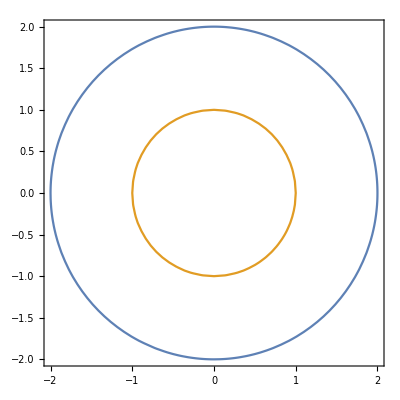

```mathematica
ContourPlot[{ 
Evaluate[ ( hyperboloid4pt1  /. Subscript[Z, 0]-> 0 /. Subscript[Z, 3]-> 0  /.  Subscript[Z, 4]-> 0   /. Λ-> 3 /. a-> 2  )]  ,
Evaluate[ ( hyperboloid4pt1  /. Subscript[Z, 0]-> 0 /. Subscript[Z, 3]-> 0  /.  Subscript[Z, 4]-> 0   /. Λ-> 3 /. a-> 1  )]
}, { Subscript[Z, 1] , -2 , 2 } , { Subscript[Z, 2] , -2 , 2 } ] 
(* Pick two different values of a  then plot constnat x and Subscript[η, 0] *)
```

```mathematica
Clear[transform4pt14]
transform4pt14 = 
Subscript[η, 0]-> a Exp[(-Subscript[t, 0])/a]
```

η_0→a ⅇ^(-t_0/a)

```mathematica
Dt[ transform4pt14 ]  /. dtReplace
```

dη_0→-ⅇ^(-t_0/a) dt_0

```mathematica
lineElement4pt13 

Clear[lineElement4pt14]
lineElement4pt14 = 
lineElement4pt13  /. transform4pt14  /. ( Dt[ transform4pt14 ]  /. dtReplace  )  // Expand // Simplify
```

(a^2 (dx^2+dy^2+dz^2-dη_0^2))/η_0^2

(dx^2+dy^2+dz^2) ⅇ^((2 t_0)/a)-dt_0^2

```mathematica
Clear[transform4pt15]
transform4pt15 = { 
Subscript[Z, 0]-> a Sinh[Subscript[t, -1]/a] Cosh[ρ],
Subscript[Z, 1]-> a Cosh[Subscript[t, -1]/a] ,
Subscript[Z, 2]->  a Sinh[Subscript[t, -1]/a] Sinh[ρ] Cos[θ],
Subscript[Z, 3]-> a Sinh[Subscript[t, -1]/a] Sinh[ρ] Sin[θ] Cos[ϕ],
Subscript[Z, 4]->   a Sinh[Subscript[t, -1]/a] Sinh[ρ] Sin[θ] Sin[ϕ]
} ;
transform4pt15 // TableForm
```

Z_0→a Cosh[ρ] Sinh[(t_-1)/a]
Z_1→a Cosh[(t_-1)/a]
Z_2→a Cos[θ] Sinh[(t_-1)/a] Sinh[ρ]
Z_3→a Cos[ϕ] Sin[θ] Sinh[(t_-1)/a] Sinh[ρ]
Z_4→a Sin[θ] Sin[ϕ] Sinh[(t_-1)/a] Sinh[ρ]

```mathematica
hyperboloid4pt1 //. transform4pt15   // Simplify  (* true *)
```

True

```mathematica
Dt[ transform4pt15 ]  /. dtReplace  // TableForm
```

dZ_0→a dρ Sinh[(t_-1)/a] Sinh[ρ]+Cosh[(t_-1)/a] Cosh[ρ] dt_-1
dZ_1→Sinh[(t_-1)/a] dt_-1
dZ_2→a dρ Cos[θ] Cosh[ρ] Sinh[(t_-1)/a]-a dθ Sin[θ] Sinh[(t_-1)/a] Sinh[ρ]+Cos[θ] Cosh[(t_-1)/a] Sinh[ρ] dt_-1
dZ_3→a dρ Cos[ϕ] Cosh[ρ] Sin[θ] Sinh[(t_-1)/a]+a dθ Cos[θ] Cos[ϕ] Sinh[(t_-1)/a] Sinh[ρ]-a dϕ Sin[θ] Sin[ϕ] Sinh[(t_-1)/a] Sinh[ρ]+Cos[ϕ] Cosh[(t_-1)/a] Sin[θ] Sinh[ρ] dt_-1
dZ_4→a dρ Cosh[ρ] Sin[θ] Sin[ϕ] Sinh[(t_-1)/a]+a dϕ Cos[ϕ] Sin[θ] Sinh[(t_-1)/a] Sinh[ρ]+a dθ Cos[θ] Sin[ϕ] Sinh[(t_-1)/a] Sinh[ρ]+Cosh[(t_-1)/a] Sin[θ] Sin[ϕ] Sinh[ρ] dt_-1

```mathematica
Clear[lineElement4pt16]
lineElement4pt16 = 
Collect[ ( lineElement  /. ( Dt[ transform4pt15 ]  /. dtReplace  ) // Expand ) , { Subscript[dt, -1]^2, dρ^2, dθ^2, dϕ^2} ]  // Simplify
```

a^2 Sinh[(t_-1)/a]^2 (dρ^2+(dθ^2+dϕ^2 Sin[θ]^2) Sinh[ρ]^2)-dt_-1^2

```mathematica
Clear[metric4pt16]
metric4pt16 = 
lineToMetric[ ( lineElement4pt16  // Expand  ) , { Subscript[dt, -1] , dρ , dθ , dϕ } ]  ;
metric4pt16 // MatrixForm
```

(-1 | 0 | 0 | 0
0 | a^2 Sinh[(t_-1)/a]^2 | 0 | 0
0 | 0 | a^2 Sinh[(t_-1)/a]^2 Sinh[ρ]^2 | 0
0 | 0 | 0 | a^2 Sin[θ]^2 Sinh[(t_-1)/a]^2 Sinh[ρ]^2)

```mathematica
eulerLagrangeEquations[ metric4pt16 , {Subscript[t, -1], ρ,θ,ϕ}, u ]  // TableForm
```

a Cosh[(t_-1[u])/a] Sinh[(t_-1[u])/a] Sinh[ρ[u]]^2 θ'[u]^2+a Cosh[(t_-1[u])/a] Sinh[(t_-1[u])/a] ρ'[u]^2+a Cosh[(t_-1[u])/a] Sin[θ[u]]^2 Sinh[(t_-1[u])/a] Sinh[ρ[u]]^2 ϕ'[u]^2+t_-1''[u]
-Cosh[ρ[u]] Sinh[ρ[u]] θ'[u]^2+(2 Coth[(t_-1[u])/a] t_-1'[u] ρ'[u])/a-Cosh[ρ[u]] Sin[θ[u]]^2 Sinh[ρ[u]] ϕ'[u]^2+ρ''[u]
(2 Coth[(t_-1[u])/a] t_-1'[u] θ'[u])/a+2 Coth[ρ[u]] θ'[u] ρ'[u]-Cos[θ[u]] Sin[θ[u]] ϕ'[u]^2+θ''[u]
(2 Coth[(t_-1[u])/a] t_-1'[u] ϕ'[u])/a+2 Cot[θ[u]] θ'[u] ϕ'[u]+2 Coth[ρ[u]] ρ'[u] ϕ'[u]+ϕ''[u]

```mathematica
Clear[transform4pt17]
transform4pt17 = {
Subscript[Z, 0]-> (1/(√2))(𝒱 + 𝒰 ) (1 - Λ/6( 𝒰 𝒱 - ξ ξ̄ ) )^-1 , 
Subscript[Z, 1]-> (1/(√2))(𝒱 - 𝒰 ) (1 - Λ/6( 𝒰 𝒱 - ξ ξ̄ ) )^-1 ,
Subscript[Z, 2]->  (1/(√2))(ξ + ξ̄ ) (1 - Λ/6( 𝒰 𝒱 - ξ ξ̄ ) )^-1 ,
Subscript[Z, 3]->  (-1/(√2))(ξ - ξ̄ ) (1 - Λ/6( 𝒰 𝒱 - ξ ξ̄ ) )^-1 ,
Subscript[Z, 4]-> a(1 + Λ/6( 𝒰 𝒱 - ξ ξ̄ ) )(1 - Λ/6( 𝒰 𝒱 - ξ ξ̄ ) )^-1
} ;
transform4pt17 // TableForm
```

Z_0→(𝒰+𝒱)/(√2 (1-1/6 Λ (𝒰 𝒱-ξ ξ̄)))
Z_1→(-𝒰+𝒱)/(√2 (1-1/6 Λ (𝒰 𝒱-ξ ξ̄)))
Z_2→(ξ+ξ̄)/(√2 (1-1/6 Λ (𝒰 𝒱-ξ ξ̄)))
Z_3→-(ξ-ξ̄)/(√2 (1-1/6 Λ (𝒰 𝒱-ξ ξ̄)))
Z_4→(a (1+1/6 Λ (𝒰 𝒱-ξ ξ̄)))/(1-1/6 Λ (𝒰 𝒱-ξ ξ̄))

```mathematica
hyperboloid4pt1
hyperboloid4pt1 /. transform4pt17
hyperboloid4pt1 /. transform4pt17 // Expand // Simplify  (* need to figure out complex variables part *)
```

-Z_0^2+Z_1^2+Z_2^2+Z_3^2+Z_4^2==a^2

(-𝒰+𝒱)^2/(2 (1-1/6 Λ (𝒰 𝒱-ξ ξ̄))^2)-(𝒰+𝒱)^2/(2 (1-1/6 Λ (𝒰 𝒱-ξ ξ̄))^2)+(ξ-ξ̄)^2/(2 (1-1/6 Λ (𝒰 𝒱-ξ ξ̄))^2)+(ξ+ξ̄)^2/(2 (1-1/6 Λ (𝒰 𝒱-ξ ξ̄))^2)+(a^2 (1+1/6 Λ (𝒰 𝒱-ξ ξ̄))^2)/(1-1/6 Λ (𝒰 𝒱-ξ ξ̄))^2==a^2

(2 𝒰 𝒱 (-3+a^2 Λ)+3 ξ^2-2 a^2 Λ ξ ξ̄+3 (ξ̄)^2)/(-6+𝒰 𝒱 Λ-Λ ξ ξ̄)==0

```mathematica
Dt[ transform4pt17 ] /. dtReplace  (* typesetting doesn't work with differentials *)
```

{dZ_0→((𝒰+𝒱) Λ (d𝒱 𝒰+d𝒰 𝒱-dξ ξ̄-d ξ ξ̄))/(6 √2 (1-1/6 Λ (𝒰 𝒱-ξ ξ̄))^2)+(d𝒰+d𝒱)/(√2 (1-1/6 Λ (𝒰 𝒱-ξ ξ̄))),dZ_1→((-𝒰+𝒱) Λ (d𝒱 𝒰+d𝒰 𝒱-dξ ξ̄-d ξ ξ̄))/(6 √2 (1-1/6 Λ (𝒰 𝒱-ξ ξ̄))^2)+(-d𝒰+d𝒱)/(√2 (1-1/6 Λ (𝒰 𝒱-ξ ξ̄))),dZ_2→(Λ (ξ+ξ̄) (d𝒱 𝒰+d𝒰 𝒱-dξ ξ̄-d ξ ξ̄))/(6 √2 (1-1/6 Λ (𝒰 𝒱-ξ ξ̄))^2)+(dξ+d ξ̄)/(√2 (1-1/6 Λ (𝒰 𝒱-ξ ξ̄))),dZ_3→-(Λ (ξ-ξ̄) (d𝒱 𝒰+d𝒰 𝒱-dξ ξ̄-d ξ ξ̄))/(6 √2 (1-1/6 Λ (𝒰 𝒱-ξ ξ̄))^2)-(dξ-d ξ̄)/(√2 (1-1/6 Λ (𝒰 𝒱-ξ ξ̄))),dZ_4→(a Λ (d𝒱 𝒰+d𝒰 𝒱-dξ ξ̄-d ξ ξ̄))/(6 (1-1/6 Λ (𝒰 𝒱-ξ ξ̄)))+(a Λ (d𝒱 𝒰+d𝒰 𝒱-dξ ξ̄-d ξ ξ̄) (1+1/6 Λ (𝒰 𝒱-ξ ξ̄)))/(6 (1-1/6 Λ (𝒰 𝒱-ξ ξ̄))^2)}

```mathematica
Clear[transform4pt20]
transform4pt20 = { 
Subscript[Z, 0]-> a Sinh[Subscript[t, b]/a] Cosh[θ] ,
Subscript[Z, 1]-> a Cosh[Subscript[t, b]/a] Cos[Subscript[z, b]] ,
Subscript[Z, 2]-> a Cosh[Subscript[t, b]/a] Sin[Subscript[z, b]] ,
Subscript[Z, 3]-> a Sinh[Subscript[t, b]/a] Sinh[θ] Cos[ϕ] ,
Subscript[Z, 4]-> a Sinh[Subscript[t, b]/a] Sinh[θ] Sin[ϕ]
} ;
transform4pt20 // TableForm
```

Z_0→a Cosh[θ] Sinh[t_b/a]
Z_1→a Cos[z_b] Cosh[t_b/a]
Z_2→a Cosh[t_b/a] Sin[z_b]
Z_3→a Cos[ϕ] Sinh[t_b/a] Sinh[θ]
Z_4→a Sin[ϕ] Sinh[t_b/a] Sinh[θ]

```mathematica
hyperboloid4pt1 //. transform4pt20  // Simplify  (* true *)
```

True

```mathematica
Dt[ transform4pt20 ]  /. dtReplace  // TableForm
```

dZ_0→a dθ Sinh[t_b/a] Sinh[θ]+Cosh[t_b/a] Cosh[θ] dt_b
dZ_1→Cos[z_b] Sinh[t_b/a] dt_b-a Cosh[t_b/a] Sin[z_b] dz_b
dZ_2→Sin[z_b] Sinh[t_b/a] dt_b+a Cos[z_b] Cosh[t_b/a] dz_b
dZ_3→a dθ Cos[ϕ] Cosh[θ] Sinh[t_b/a]-a dϕ Sin[ϕ] Sinh[t_b/a] Sinh[θ]+Cos[ϕ] Cosh[t_b/a] Sinh[θ] dt_b
dZ_4→a dθ Cosh[θ] Sin[ϕ] Sinh[t_b/a]+a dϕ Cos[ϕ] Sinh[t_b/a] Sinh[θ]+Cosh[t_b/a] Sin[ϕ] Sinh[θ] dt_b

```mathematica
Collect[ ( lineElement /. ( Dt[ transform4pt20 ]  /. dtReplace ) // Expand ) , { Subscript[dt, b]^2 , Subscript[dz, b]^2 , dθ^2, dϕ^2 } ] // Simplify
```

-dt_b^2+1/2 a^2 ((2 dθ^2-dϕ^2+dϕ^2 Cosh[2 θ]) Sinh[t_b/a]^2+2 Cosh[t_b/a]^2 dz_b^2)

```mathematica
Clear[metric4pt21]
metric4pt21 = 
lineToMetric[ Collect[ ( lineElement /. ( Dt[ transform4pt20 ]  /. dtReplace ) // Expand ) , { Subscript[dt, b]^2 , Subscript[dz, b]^2 , dθ^2, dϕ^2 } ] , { Subscript[dt, b] , Subscript[dz, b] , dθ , dϕ } ]  // Simplify  ;
metric4pt21 // MatrixForm
```

(-1 | 0 | 0 | 0
0 | a^2 Cosh[t_b/a]^2 | 0 | 0
0 | 0 | a^2 Sinh[t_b/a]^2 | 0
0 | 0 | 0 | a^2 Sinh[t_b/a]^2 Sinh[θ]^2)

```mathematica
eulerLagrangeEquations[ metric4pt21 , {Subscript[t, b], Subscript[z, b], θ, ϕ} , u ]  // TableForm
```

a Cosh[t_b[u]/a] Sinh[t_b[u]/a] z_b'[u]^2+a Cosh[t_b[u]/a] Sinh[t_b[u]/a] θ'[u]^2+a Cosh[t_b[u]/a] Sinh[t_b[u]/a] Sinh[θ[u]]^2 ϕ'[u]^2+t_b''[u]
(2 Tanh[t_b[u]/a] t_b'[u] z_b'[u])/a+z_b''[u]
(2 Coth[t_b[u]/a] t_b'[u] θ'[u])/a-Cosh[θ[u]] Sinh[θ[u]] ϕ'[u]^2+θ''[u]
(2 Coth[t_b[u]/a] t_b'[u] ϕ'[u])/a+2 Coth[θ[u]] θ'[u] ϕ'[u]+ϕ''[u]

```mathematica
Clear[differentials]
differentials = { Subscript[dt, b] , Subscript[dz, b] , dθ , dϕ }
```

{dt_b,dz_b,dθ,dϕ}

```mathematica
lineElement4pt21 = Collect[ Sum[ metric4pt21[[i,i]]* ( differentials[[i]] )^2 , { i , 1 , 4 } ]   , a^2 Sinh[Subscript[t, b]/a]^2  ]
```

a^2 Sinh[t_b/a]^2 (dθ^2+dϕ^2 Sinh[θ]^2)-dt_b^2+a^2 Cosh[t_b/a]^2 dz_b^2

```mathematica
Clear[transform4pt22]
transform4pt22 = { 
Subscript[Z, 0]-> a Sinh[Subscript[t, k]/a] Cosh[Subscript[z, k]] ,
Subscript[Z, 1]-> a Sinh[Subscript[t, k]/a] Sinh[Subscript[z, k]] ,
Subscript[Z, 2]-> a Cosh[Subscript[t, k]/a] Cos[θ] ,
Subscript[Z, 3]-> a Cosh[Subscript[t, k]/a] Sin[θ] Cos[ϕ] ,
Subscript[Z, 4]->  a Cosh[Subscript[t, k]/a] Sin[θ] Sin[ϕ]
} ;
transform4pt22 // TableForm
```

Z_0→a Cosh[z_k] Sinh[t_k/a]
Z_1→a Sinh[t_k/a] Sinh[z_k]
Z_2→a Cos[θ] Cosh[t_k/a]
Z_3→a Cos[ϕ] Cosh[t_k/a] Sin[θ]
Z_4→a Cosh[t_k/a] Sin[θ] Sin[ϕ]

```mathematica
hyperboloid4pt1 //. transform4pt22  // Simplify  (* true *)
```

True

```mathematica
Dt[ transform4pt22 ]  /. dtReplace  // TableForm
```

dZ_0→Cosh[t_k/a] Cosh[z_k] dt_k+a Sinh[t_k/a] Sinh[z_k] dz_k
dZ_1→Cosh[t_k/a] Sinh[z_k] dt_k+a Cosh[z_k] Sinh[t_k/a] dz_k
dZ_2→-a dθ Cosh[t_k/a] Sin[θ]+Cos[θ] Sinh[t_k/a] dt_k
dZ_3→a dθ Cos[θ] Cos[ϕ] Cosh[t_k/a]-a dϕ Cosh[t_k/a] Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] Sinh[t_k/a] dt_k
dZ_4→a dϕ Cos[ϕ] Cosh[t_k/a] Sin[θ]+a dθ Cos[θ] Cosh[t_k/a] Sin[ϕ]+Sin[θ] Sin[ϕ] Sinh[t_k/a] dt_k

```mathematica
Collect[ ( lineElement /. ( Dt[ transform4pt22 ]  /. dtReplace  )  // Expand )  , { Subscript[dt, k]^2, Subscript[dz, k]^2, dθ^2, dϕ^2} ]
```

dθ^2 (a^2 Cos[θ]^2 Cos[ϕ]^2 Cosh[t_k/a]^2+a^2 Cosh[t_k/a]^2 Sin[θ]^2+a^2 Cos[θ]^2 Cosh[t_k/a]^2 Sin[ϕ]^2)+dϕ^2 (a^2 Cos[ϕ]^2 Cosh[t_k/a]^2 Sin[θ]^2+a^2 Cosh[t_k/a]^2 Sin[θ]^2 Sin[ϕ]^2)+dθ (-2 a Cos[θ] Cosh[t_k/a] Sin[θ] Sinh[t_k/a]+2 a Cos[θ] Cos[ϕ]^2 Cosh[t_k/a] Sin[θ] Sinh[t_k/a]+2 a Cos[θ] Cosh[t_k/a] Sin[θ] Sin[ϕ]^2 Sinh[t_k/a]) dt_k+(-Cosh[t_k/a]^2 Cosh[z_k]^2+Cos[θ]^2 Sinh[t_k/a]^2+Cos[ϕ]^2 Sin[θ]^2 Sinh[t_k/a]^2+Sin[θ]^2 Sin[ϕ]^2 Sinh[t_k/a]^2+Cosh[t_k/a]^2 Sinh[z_k]^2) dt_k^2+(a^2 Cosh[z_k]^2 Sinh[t_k/a]^2-a^2 Sinh[t_k/a]^2 Sinh[z_k]^2) dz_k^2

```mathematica
Clear[metric4pt23]
metric4pt23 = 
lineToMetric[
( Collect[ ( lineElement /. ( Dt[ transform4pt22 ]  /. dtReplace  )  // Expand )  , { Subscript[dt, k]^2, Subscript[dz, k]^2, dθ^2, dϕ^2} ]  ) , { Subscript[dt, k] , Subscript[dz, k] , dθ , dϕ } ]  // Simplify  ;
metric4pt23 // MatrixForm
```

(-1 | 0 | 0 | 0
0 | a^2 Sinh[t_k/a]^2 | 0 | 0
0 | 0 | a^2 Cosh[t_k/a]^2 | 0
0 | 0 | 0 | a^2 Cosh[t_k/a]^2 Sin[θ]^2)

```mathematica
eulerLagrangeEquations[ metric4pt23 , {Subscript[t, k], Subscript[z, k], θ,ϕ} , u ]  // TableForm
```

a Cosh[t_k[u]/a] Sinh[t_k[u]/a] z_k'[u]^2+a Cosh[t_k[u]/a] Sinh[t_k[u]/a] θ'[u]^2+a Cosh[t_k[u]/a] Sin[θ[u]]^2 Sinh[t_k[u]/a] ϕ'[u]^2+t_k''[u]
(2 Coth[t_k[u]/a] t_k'[u] z_k'[u])/a+z_k''[u]
(2 Tanh[t_k[u]/a] t_k'[u] θ'[u])/a-Cos[θ[u]] Sin[θ[u]] ϕ'[u]^2+θ''[u]
(2 Tanh[t_k[u]/a] t_k'[u] ϕ'[u])/a+2 Cot[θ[u]] θ'[u] ϕ'[u]+ϕ''[u]

```mathematica
Clear[differentials]
differentials = { Subscript[dt, k] ,  Subscript[dz, k] , dθ , dϕ }
```

{dt_k,dz_k,dθ,dϕ}

```mathematica
Clear[lineElement4pt23]
lineElement4pt23 =  Collect[ Sum[ metric4pt23[[i,i]]* ( differentials[[i]] )^2 , { i , 1 , 4 } ] , a^2  Cosh[Subscript[t, k]/a]^2 ]
```

a^2 Cosh[t_k/a]^2 (dθ^2+dϕ^2 Sin[θ]^2)-dt_k^2+a^2 Sinh[t_k/a]^2 dz_k^2